```mathematica
(*Exercise 1*)
```

```mathematica
coefsToFind = {a0,a1,a2, b1,b2};
generalTrigPoly[x_]:=a0+a1*Sin[x]+b1*Cos[x]+a2*Sin[2*x]+b2*Cos[2*x];
originalNodes ={0, 1.5,3,4,6};
originalValues = {0,1,1.5,4,2};
pointPlot = ListPlot[Transpose[{originalNodes, originalValues}], PlotStyle->Orange];
```

Case A

No linear swap required.

```mathematica
caseACoefs = Solve[{
generalTrigPoly[originalNodes[[1]]]==originalValues[[1]],
generalTrigPoly[originalNodes[[2]]]==originalValues[[2]],
generalTrigPoly[originalNodes[[3]]]==originalValues[[3]],
generalTrigPoly[originalNodes[[4]]]==originalValues[[4]],
generalTrigPoly[originalNodes[[5]]]==originalValues[[5]]}, coefsToFind]
{a0->2.518278,a1->-3.041215,a2->-1.565509,b1->-0.713502,b2->-1.804775}
```

```mathematica
substituedApproximationA[x_]= generalTrigPoly[x]/.caseACoefs[[1]]
2.518278-0.713502 Cos[x]-1.804775 Cos[2 x]-3.041215 Sin[x]-1.565509 Sin[2 x]
```

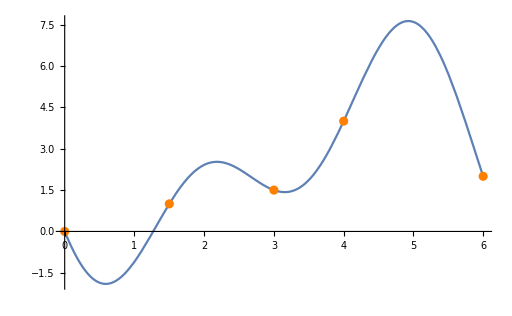
```mathematica
approximationAPlot = Plot[substituedApproximationA[x], {x, 0, 6}, PlotRange->Full];
Show[{approximationAPlot, pointPlot}]
-Graphics-
```

Case B

Linear swap: [0, 8] > [0, 2Pi] : t=4/Pi*x

```mathematica
swappedNodes= {0, 4/Pi*(1.5), 4/Pi*(3),  4/Pi*(4), 4/Pi*(6)};
swappedPointPlot = ListPlot[Transpose[{swappedNodes, originalValues}], PlotStyle->Orange];
```

```mathematica
caseBCoefs = Solve[{
generalTrigPoly[swappedNodes[[1]]]==originalValues[[1]],
generalTrigPoly[swappedNodes[[2]]]==originalValues[[2]],
generalTrigPoly[swappedNodes[[3]]]==originalValues[[3]],
generalTrigPoly[swappedNodes[[4]]]==originalValues[[4]],
generalTrigPoly[swappedNodes[[5]]]==originalValues[[5]]}, coefsToFind]
```

{{a0→1.2512,a1→-1.39792,a2→0.372895,b1→0.732238,b2→-1.98344}}

```mathematica
substituedApproximationB[x_] = generalTrigPoly[x]/.caseBCoefs[[1]]
1.251201219578497+0.7322381586996939 Cos[x]-1.983439378278191 Cos[2 x]-1.3979170261975025 Sin[x]+0.3728950454894465 Sin[2 x]
```

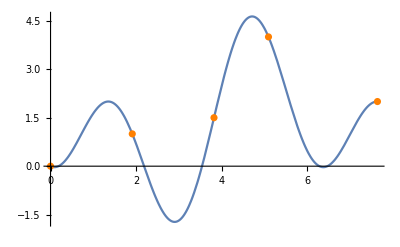

```mathematica
approximationBPlot = Plot[substituedApproximationB[x], {x, 0, 4/Pi*(6)}];
Show[{approximationBPlot, swappedPointPlot}]
```

```mathematica
(*Exercise 2*)
```

```mathematica
ex2Nodes = {2,4,6,7,10,11,14,17,20};
ex2Values= {4,5,6,7,8,8,11,10,12};
```

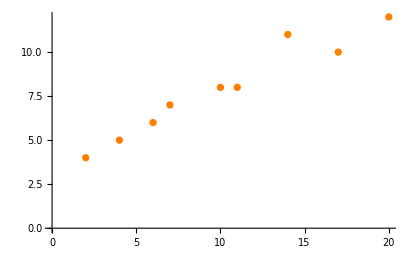
```mathematica
ex2NodePlot = ListPlot[Transpose[{ex2Nodes,ex2Values}], PlotStyle->Orange];
Show[ex2NodePlot]

(*I can't determine what kind of function I should use for approximation, that is why I initially plot out the nodes to see what function is best suited for the task.*)

-Graphics-
(*From the node plot I conclude that a quadratic function would work well for the approximation*)
```

```mathematica
basePoly[x_]:= a*x^2+b*x+c;
```

```mathematica
derivFunc[a_,b_,c_] :=∑_(i=1)^Length[ex2Nodes] (a*(ex2Nodes[[i]])^2+b*ex2Nodes[[i]] + c-ex2Values[[i]])^2;
ex2DerivA[a_,b_,c_]= D[derivFunc[a,b,c], a];
ex2DerivB[a_,b_,c_] = D[derivFunc[a,b,c], b];
ex2DerivC[a_,b_,c_] = D[derivFunc[a,b,c], c];
```

```mathematica
ex2Coefs = Solve[{ex2DerivA[a,b,c] == 0, ex2DerivB[a,b,c]==0, ex2DerivC[a,b,c] == 0}, {a,b,c}];
{{a->-11440/1294719,b->816452/1294719,c->1165991/431573}};
```

```mathematica
ex2SubstPoly[x_]  = basePoly[x]/.ex2Coefs[[1]];
ex2SubstPoly[x];
1165991/431573+(816452 x)/1294719-(11440 x^2)/1294719;
```

```mathematica
ex2ApproxFuncPlot = Plot[ex2SubstPoly[x], {x,1,20}];
Show[{ex2NodePlot, ex2ApproxFuncPlot}]

-Graphics-
```

```mathematica
(*Exercise 3*)
```

```mathematica
equation1Value= 1;
equation2Value = 5;
equation3Value = 17;
```

```mathematica
equation1[x_,y_] = x+2*y+equation1Value;
equation2[x_,y_]  =x-y + equation2Value;
equation3[x_,y_] =3*x+4*y+equation3Value;
```

```mathematica
errorEquation[x_, y_] = (equation1[x,y])^2+(equation2[x,y])^2+(equation3[x,y])^2;
errorEquation[x,y]
(5+x-y)^2+(1+x+2 y)^2+(17+3 x+4 y)^2
```

```mathematica
derivByX[x_,y_] = D[errorEquation[x,y], x];
derivByY[x_,y_] = D[errorEquation[x,y], y];
```

```mathematica
BestResults = Solve[{derivByX[x,y]==0, derivByY[x,y]==0}, {x, y}]
{{x->-176/31,y->13/31}}
```

```mathematica
ClosestPoint = Point[{-176/31, 13/31}];
```

```mathematica
equ1ViaY[y_] = 1-2*y;
equ2ViaY[y_] = y+5;
equ3ViaY[y_] = (17-4*y)/3;
```

```mathematica
bestPoint=Graphics[{PointSize[Large],Red,ClosestPoint}];
functionsPlot = Plot[{equ1ViaY[y], equ2ViaY[y], equ3ViaY[y]}, {y, -20,20}, PlotLabel->"Approximation visualization", PlotLabels->Automatic, PlotStyle->Thick];
Show[{functionsPlot,bestPoint}]
```

-Graphics-

```mathematica
(*Exercise 4*)
```

```mathematica
functionToApproximate[x_] = Sin[x];
weight = 1;
intervalStart = 0;
intervalEnd = Pi/2;
basePoly[x_]:= a*x^2 + b*x+c;
```

```mathematica
polyToMinimize[a_,b_,c_]:= (Integrate[weight*(functionToApproximate[x]-basePoly[x])^2, {x, intervalStart,intervalEnd}])^(1/2);
polyToMinimize[a,b,c];
```

```mathematica
√(4 a-2 c+1/4 (1+2 c^2) π+1/4 b c π^2+1/24 (b^2+2 a c) π^3+1/32 a b π^4+(a^2 π^5)/160-2 (b+a π))
```

```mathematica
DerivByA[a_,b_,c_]=D[polyToMinimize[a,b,c], a];
DerivByB[a_,b_,c_]=D[polyToMinimize[a,b,c], b];
DerivByC[a_,b_,c_]= D[polyToMinimize[a,b,c], c];
```

```mathematica
bestCoefs = NSolve[{DerivByA[a,b,c]==0, DerivByB[a,b,c]==0, DerivByC[a,b,c]==0},{a,b,c}];
{{a->-0.33824,b->1.19574,c->-0.02432}};
```

```mathematica
bestApproximationPoly[x_]= basePoly[x]/.bestCoefs[[1]];
-0.02432+1.19574*x-0.33824* x^2;
```

```mathematica
averageQuadraticDifference = (Integrate[weight*(functionToApproximate[x]-bestApproximationPoly[x])^2, {x, intervalStart,intervalEnd}])^(1/2);
0.01050;
```

```mathematica
regularDifference = Maximize[Abs[(functionToApproximate[x] - bestApproximationPoly[x])],intervalStart≤x≤ intervalEnd,x];
{0.02432,{x->0.}};
```

```mathematica
comparisonPlot = Plot[{functionToApproximate[x], bestApproximationPoly[x]}, {x, intervalStart, intervalEnd}, PlotLabel->"Approximation visualization", PlotLabels->Automatic,  Filling->{1->{2}}]
-Graphics-
```

```mathematica
(*Exercise 5*)
```

```mathematica
funcToApproxIntegrate[x_] = (1-E^-x);
intervalStart = 0;
intervalEnd = 4;
```

```mathematica
secondDeriv[x_]  = D[funcToApproxIntegrate[x], {x,2}];
-ⅇ^-x;
```

```mathematica
fourthDeriv[x_]= D[funcToApproxIntegrate[x], {x,2}];
-ⅇ^-x;
```

```mathematica
rectErr[n_]=Abs[secondDeriv[intervalStart]]/(24*n^2)*(intervalEnd-intervalStart)^3;
trapErr[n_] = Abs[-secondDeriv[intervalStart]]/(12*n^2)*(intervalEnd-intervalStart)^3;
simpErr[n_] = Abs[fourthDeriv[intervalStart]]/(2880*n^4)(intervalEnd-intervalStart)^5;
```

```mathematica
ApproximateWithRect[epsAccuracy_]:=(
rectBestN = Floor[Sqrt[ rectErr[epsAccuracy]]];
rectApproximationResult = 0;
rectNodes =Subdivide[0.,4.,rectBestN];
For[i = 2, i≤  Length[rectNodes], i++, rectApproximationResult+=funcToApproxIntegrate[(rectNodes[[i]]+rectNodes[[i-1]])/2]];
rectApproximationResult=((intervalEnd-intervalStart)/rectBestN)*rectApproximationResult
);
```

```mathematica
ApproximateWithTrap[epsAccuracy_]:=(
trapBestN = Floor[Sqrt[ trapErr[epsAccuracy]]];
trapApproximationResult = 0;
trapNodes =Subdivide[4,trapBestN];
For[i = 2, i≤  Length[trapNodes], i++, trapApproximationResult+=funcToApproxIntegrate[trapNodes[[i]]]+funcToApproxIntegrate[trapNodes[[i-1]]]];
trapApproximationResult=((intervalEnd-intervalStart)/(2*trapBestN))*trapApproximationResult
);
```

```mathematica
ApproximateWithSimp[epsAccuracy_]:=(
simpBestN = Floor[Sqrt[simpErr[epsAccuracy]]];
simpApproximationResult = 0;
simpNodes =Subdivide[4,simpBestN];
For[i = 2, i≤  Length[simpNodes], i++, simpApproximationResult+=funcToApproxIntegrate[simpNodes[[i]]]+4*funcToApproxIntegrate[(simpNodes[[i]]+simpNodes[[i-1]])/2]+funcToApproxIntegrate[simpNodes[[i-1]]]];
simpApproximationResult*((intervalEnd-intervalStart)/(6*simpBestN))
);
```

```mathematica
rectApprox = ApproximateWithRect[10^-3];
```

```mathematica
trapApprox = ApproximateWithTrap[10^-3];
```

```mathematica
simpApprox = ApproximateWithSimp[10^-3];
```

```mathematica
expectedResult = Integrate[funcToApproxIntegrate[x],{x,0,4}];
```

```mathematica
rectApprox //N
3.018567
```

```mathematica
trapApprox //N
3.018070
```

```mathematica
simpApprox//N
3.018314
```

```mathematica
expectedResult//N
3.018315
```

```mathematica
(*Exercise 6*)
```

```mathematica
RectangleQuadrature[funcToApproximate_, a_,b_, nodes_]:= 
(
numberOfNodes = Length[nodes];
approximationResult = 0;
For[i = 2, i <=numberOfNodes, i ++, approximationResult+= funcToApproximate[(nodes[[i]]+nodes[[i-1]])/2]];
approximationResult*(b-a)/numberOfNodes
);
```

```mathematica
givenFuncToIntegrate[x_]:= E^Sin[x]-2 x^2;
equallySpacedNodes = {0, 0.2,0.4,0.6,0.8, 1};
ApproximationResultFromFunction = RectangleQuadrature[givenFuncToIntegrate, 0, 1, equallySpacedNodes]
0.8095328029161283
```

```mathematica
(*Excpected result from directly using the rectangle quadrature formula. I use this to check the corectness of the RectangleQuadrature function above.*)
a = 0;
b = 1;
DirectRectFormulaResult = (b-a)/Length[equallySpacedNodes]*Sum[givenFuncToIntegrate[(equallySpacedNodes[[i]]+equallySpacedNodes[[i-1]])/2], {i, 2, Length[equallySpacedNodes]}]
0.8095328029161283
```

```mathematica
(*Exercise 7*)
```

```mathematica
xNodes = {-3,-2,-1,0,1,2,3};
```

```mathematica
sValue = Length[xNodes];
```

```mathematica
matrixA = Table[∑_(i=1)^sValue (xNodes[[i]])^(m+j), {m,0,3}, {j,0,3}]
```

Power::indet: Indeterminate expression 0^0 encountered.

{{Indeterminate,0,28,0},{0,28,0,196},{28,0,196,0},{0,196,0,1588}}

```mathematica
(*Exercise 8*)
```

```mathematica
res0=Integrate[x^0, {x,-1,1}];
res1=Integrate[x^1, {x,-1,1}];
res2=Integrate[x^2, {x,-1,1}];
res3=Integrate[x^3, {x,-1,1}];
res4=Integrate[x^4, {x,-1,1}];
res5=Integrate[x^5, {x,-1,1}];
```

```mathematica
formulaCoefs = Solve[{
A1+A1+A2+A3== res0,
A1*x1+A2*x2+A3*x3== res1,
A1*x1^2+A2*x2^2+A3*x3^2== res2,
A1*x1^3+A2*x2^3+A3*x3^3== res3,
A1*x1^4+A2*x2^4+A3*x3^4== res4,
A1*x1^5+A2*x2^5+A3*x3^5== res5},
{A1,A2,A3,x1,x2,x3}
]
```

{{A1→5/9,A2→5/9,A3→1/3,x1→√(3/5),x2→-√(3/5),x3→0},{A1→5/9,A2→5/9,A3→1/3,x1→-√(3/5),x2→√(3/5),x3→0},{A1→5/9,A2→1/3,A3→5/9,x1→√(3/5),x2→0,x3→-√(3/5)},{A1→4/9,A2→5/9,A3→5/9,x1→0,x2→√(3/5),x3→-√(3/5)},{A1→8/9,A2→5/9,A3→-1/3,x1→-√(3/5),x2→√(3/5),x3→-√(3/5)},{A1→8/9,A2→-1/3,A3→5/9,x1→√(3/5),x2→√(3/5),x3→-√(3/5)},{A1→5/9,A2→1/3,A3→5/9,x1→-√(3/5),x2→0,x3→√(3/5)},{A1→4/9,A2→5/9,A3→5/9,x1→0,x2→-√(3/5),x3→√(3/5)},{A1→8/9,A2→-1/3,A3→5/9,x1→-√(3/5),x2→-√(3/5),x3→√(3/5)},{A1→8/9,A2→5/9,A3→-1/3,x1→√(3/5),x2→-√(3/5),x3→√(3/5)}}

```mathematica
A1=0.5555;
A2=0.8888;
A3=0.5555;
x1=0.7745;
x2=0;
x3=-0.7745;
```

Linear swap: x= 0.5*t + 0.5 & dx = 0.5*dt

```mathematica
givenFunction[x_]:=E^Sin[x]-2 x^2;
givenFuncWithSwap[t_]:= (E^Sin[0.5*t+0.5]-2*(0.5*t+0.5)^2)*0.5;
```

```mathematica
approximation = A1*givenFuncWithSwap[x1] + A2*givenFuncWithSwap[x2]+A3*givenFuncWithSwap[x3]
0.9651
```

```mathematica
expectedResult = NIntegrate [givenFunction[x], {x,0,1}]
0.9652
```

```mathematica
(*Exercise 9*)
```

```mathematica
weight[x_]:= 1/Sqrt[1-x^2];
```

```mathematica
P0[x_] := a;
P1[x_] := a*x+b;
P2[x_] :=a*x^2+b*x+c;
```

```mathematica
(*Finding b for P1*)
Integrate[P0[x]*P1[x]*weight[x], {x,-1,1}] ==0
```

```mathematica
(*Finding b & c for P2*)
Solve[{Integrate[P0[x]*P2[x]*weight[x], {x,-1,1}] ==0,Integrate[P1[x]*P2[x]*weight[x], {x,-1,1}] ==0}, {b,c}];
```